# Quantum Mechanics

## Part II. Quantum Entanglement

## Information Theory

### Classical Information

#### Probability Theory

A deterministic variable x must represent the some definite value (even if the value is not necessarily known). Example: if 2x+1=5, then x=2.

A random variable X defines a support space 𝒳 in which each possible values x∈𝒳 is assigned a probability p(x)≡Pr(X=x).

The expectation value (mean, average) of a random variable X is the average of all possible values weighted by their probabilities

⟨x⟩=𝔼[X]=∑_(x∈𝒳) x p(x).

The variance of a random variable X is the expectation value of the squared deviation of X from its mean 𝔼[X].

var(X)=𝔼[(X-𝔼[X])^2]=⟨x^2⟩-⟨x⟩^2.

A deterministic variable x can be viewed as a special limit of a random variable X, whose probability is concentrated at one fixed value x_*.

p(x)=Pr(X=x)=Piecewise[{{1, x=x_*}, {0, x≠x_*}}].

#### Observation Theory

A Bayesian (subjectivism) view of probability:

Probability assignment is a means to describe our state of knowledge about the random variable X.

The probability assignment can be updated, if our state of knowledge is changed by observations (given new evidence from observations).

A (full) observation of a random variable X uniquely determines a outcome value x_*∈𝒳, such outcome will be observed with the probability p(x_*).

Before observing X=x_*, the probability distribution p(x) is called the prior probability.

After observing X=x_*, the probability distribution will collapse to the posterior probability p(x|X=x_*) (reads: the probability of x given the observation X=x_*)

p(x|X=x_*)=Piecewise[{{1, if x=x_*,}, {0, else.}}]

If we continue to observe X again, we would obtain X=x_* for sure, based on the updated probability p(x|X=x_*).

Observation removes the uncertainty of a random variable, making it deterministic. Repeated observations will only confirm the previous observation outcome. The observation outcome is verifiable ⇒ it qualifies as a piece of knowledge.

Example:

Rolling a dice (𝒳={1,2,3,4,5,6}) and observe X=2.

Prior probability:

x | 1 | 2 | 3 | 4 | 5 | 6
p(x) | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6

Posterior probability:

x | 1 | 2 | 3 | 4 | 5 | 6
p(x|X=2) | 0 | 1 | 0 | 0 | 0 | 0

Of course, the observation of X=2 is only one possible outcome. If other possible outcome is observed instead, the posterior probability will be different.

#### Information Theory

The amount of information that we gain from a specific observation (observing X and obtaining X=x_*) is the negative log-probability associated with the observation event

I(X=x_*)=-log Pr(X=x_*)=-log p(x_*).

Intuitions:

If p(x_*)=1, we already know for certain that X=x_*, further observing X=x_* will not bring us new knowledge, thus we are not gaining more information from the observation, and I(X=x_*)=0 in this case.

If p(x_*)→0, observing X=x_* is a rare event. But if the rare event happens, it would bring us a big surprise (a lot of knowledge), because base on the observation, a large amount of other possibilities (of X≠x_*) can be ruled out, which is very informative. So I(X=x_*)→+∞ in this case.

Examples:

Tossing a coin (𝒳={head,tail}) and observe X=head.

x | head | tail
p(x) | 1/2 | 1/2

Information gained from observation

I(X=head)=-log(1/2)=log 2=1 bit.

log 2 information is also called one bit of information (1 bit=log 2 is widely used as the information unit in information science), it is the amount of information obtained from knowing the answer of a yes-or-no question.

Observing an unknown bit string of length n=3 and obtain (say) X=010

x | 000 | 001 | 010 | 011 | 100 | 101 | 110 | 111
p(x) | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8

Information gained from observation

I(X=010)=-log(1/8)=3 log 2=3 bit.

The observation specifies one outcome from eight equally likely outcomes. To determine the bit string 010, equivalently, we need to ask three yes-or-no questions (is the 1st/2nd/3rd bit 0?). Answering each of the question will give us one bit of information about the unknown string. So the observation gives us totally three bits of information all at once.

In general, observing an unknown bit string of length n will provide n bits of information about the string, as it determines one outcome from 2^n equally likely outcomes. The probability associated with the particular observation is

p=(1/2)^n⇒-log p=n log 2=n bit=I.

So the information I(X=x_*) that we gain from observing X=x_* should be defined to be the negative logarithm of the probability p(x_*) for such observation event to happen.

I(X=x_*)=-log p(x_*)

Why logarithm? Probability is multiplicative, while information is additive. The logarithm is only correct function to convert multiplication to addition.

Observing a random variable X (𝒳={a,b,c,d}) associated with the following (prior) probability

x | a | b | c | d
p(x) | 1/2 | 1/4 | 1/8 | 1/8.

Information can be different for different observation outcomes

I(X=a)=-log(1/2)=log 2=1 bit,
I(X=b)=-log(1/4)=2log 2=2 bit,
I(X=c)=-log(1/8)=3 log 2=3 bit,
I(X=d)=-log(1/8)=3 log 2=3 bit.

However, different outcome happens with different probability. What is amount of information that we can obtained from observing X on average?

I(X)=I(X=a)p(a)+I(X=b)p(b)+I(X=c)p(c)+I(X=d)p(d)
=(1×1/2+2×1/4+3×1/8+3×1/8)bit
=1.75 bit.

In conclusion, given a random variable X, the expected information gained from a (full) observation of X is

I(X)=-⟨log p(x)⟩=-∑_(x∈𝒳) p(x)log p(x).

#### Entropy

The Shannon entropy of a random variable X measures its uncertainty (randomness), which is defined based on its probability distribution

S(X)=-∑_(x∈𝒳) p(x)log p(x).

Entropy is always non-negative (follows from 0<=p(x)<=1)

S(X)≥0.

S(X)=0 means the value of X is known for certain (no randomness).

Large S(X) indicates large uncertainty in X.

Entropy can change under observation, as observation can remove (or reduce) the uncertainty of a random variable.

Example:

A binary random variable X (with 𝒳={false,true})

p(false)=1-p, 
p(true)=p,

where 0<=p<=1. Entropy of X

S(X)=-p log p-(1-p)log (1-p).

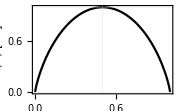

```mathematica
Plot[-(p Log[p]+(1-p)Log[1-p])/Log[2],{p,0,1},PlotStyle->Black,FrameLabel->{"\!\(p\)","\!\(S(X)\) [bit]"},GridLines->{{0.5},{0,1}},ImageSize->180]
```

S(X)=0 when p=0 (X=false for sure) or p=1 (X=true for sure).

S(X) is maximized at p=1/2, where X is most uncertain. The maximum entropy of a binary random variable is 1 bit.

Rolling a dice (𝒳={1,2,3,4,5,6}) and observe X=2.

x | 1 | 2 | 3 | 4 | 5 | 6 |  
p(x) | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | (prior)
p(x|X=2) | 0 | 1 | 0 | 0 | 0 | 0 | (posterior)

Entropy of X before the observation (the prior entropy)

S(X_prior)=-(1/6 log(1/6))×6=log 6.

Entropy of X after the observation (the posterior entropy)

S(X_post)=- ((0log 0)×5+1 log 1)=0.

Note: 0 log 0 =0 (as it should be understood as the limit lim_(x->0) x log x=0), and 1log 1=0 (because log 1=0).

Expected information gain from the observation

I(X)=(1/6 log(1/6))×6=log 6.

Relation between entropy and information.

Observation changes the probability distribution (i.e. the state of knowledge)

| X_prior | →^observe | X_post
probability | p(x) |   | p(x|X)
entropy | S(X_prior) |   | S(X_post)
  | more |   | less

The entropy change is the negative of the information gain

ΔS=S(X_post)-S(X_prior)=-I(X).

Conclusion: entropy = negative information.

### Quantum Information

#### Pure and Mixed States

A pure state describes a deterministic quantum system, modeled by

a single state vector (ket state) ψ,

or the state projector (pure state density matrix)

ρ̂= (𝒫̂)_ψ:=ψψ.

A mixed state describes a random quantum system, consists of a random ensemble of distinct states, in which each state ϕ appears with the probability p(ϕ).

The mixed state is modeled by a density matrix (density operator)  ρ, defined as the ensemble average of the state projectors

ρ̂=𝔼_ϕ[(𝒫̂)_ϕ]=∑_ϕ p(ϕ)ϕϕ.

A density matrix should satisfy the following properties

Hermitian:  (ρ̂)^†=ρ̂.

Normalization (trace one): Tr ρ̂=1.

Positive (semi)definite: ∀ψ:ψ ρ̂ ψ≥0.

A pure state ψ can be viewed a special limit of a mixed state  ρ̂, when the density matrix factorizes as

ρ̂= ψψ.

Meaning that the probability p(ϕ) concentrated at on fixed state ϕ=ψ. Not every density matrix can be expressed in the form of ψψ ⇒ A density matrix is more general than a state vector.

Definition of mixed state: a mixed state is a quantum state described by a density matrix  ρ̂ that can not be written as the pure state form ψψ.

Example: Polarization of photon

Examples of pure states:

σ^z basis states: horizontal and vertical polarizations

≏(1
0), ≏(0
1).

σ^x basis states: 45° polarizations

≏1/(√2)(1
1), ≏1/(√2)(1
-1).

σ^y basis states: circular polarizations

≏1/(√2)(1
ⅈ), ≏1/(√2)(1
-ⅈ).

Linear polarization along θ angle (with respect to x-axis)

θ≏(cos θ
sin θ)⇒(ρ̂)_θ=θθ≏(cos^2 θ | cos θ sin θ
cos θ sin θ | sin^2 θ).

Natural light: an ensemble of all possible polarizations with equal probability ⇒ maximally mixed state

(ρ̂)_𝒩=∫(ⅆ θ)/(2π)(ρ̂)_θ≏1/2(1 | 0
0 | 1).

This is an example of a mixed state.

Show that it is impossible to express  (ρ̂)_𝒩 as ψψ, hence  (ρ̂)_𝒩 is indeed a mixed state.

Prove by contradiction: suppose  (ρ̂)_𝒩 can be written as |ψ⟩⟨ψ|, then there must exist

ψ≏(ψ_0
ψ_1),

such that

(ρ̂)_𝒩=ψψ≏((|ψ_0|)^2 | ψ_0 ψ_1^*
ψ_1 ψ_0^* | (|ψ_1|)^2).

On the other hand, we are given

(ρ̂)_𝒩≏1/2(1 | 0
0 | 1).

For Eq. (DisplayFormulaNumbered) to be consistent with Eq. (DisplayFormulaNumbered), we must have the following equalities

(|ψ_0|)^2=(|ψ_1|)^2=1/2,
ψ_0 ψ_1^*=ψ_1 ψ_0^*=0.

Now consider what should the quantity (|ψ_0|)^2(|ψ_1|)^2 be.

One one hand

(|ψ_0|)^2(|ψ_1|)^2=(|ψ_0|)^2×(|ψ_1|)^2=1/2×1/2=1/4.

On the other hand

(|ψ_0|)^2(|ψ_1|)^2=(ψ_0 ψ_1^*)×(ψ_1 ψ_0^*)=0×0=0.

(|ψ_0|)^2(|ψ_1|)^2 can not simultaneously be 1/4 and 0. Thus there is no valid solution for ψ_0 and ψ_1, i.e. there is no such state ψ that provides the factorization of  (ρ̂)_𝒩.

The density matrix description of light polarization is also known as the Jones matrix.

#### Observable Expectation Value

Density matrix enables us to think about the expectation value of an observable O in a unified manner for both pure and mixed states.

Let Ô be a Hermitian operator describing the observable O,

let  ρ̂ be the density matrix describing the state of a quantum system,

observing O on the quantum system, the expectation value of O is given by

⟨O⟩=Tr ρ̂ Ô.

Arguments:

For pure state ρ̂=ψψ,

⟨O⟩=ψ Ô ψ=Trψψ Ô=Tr ρ̂ Ô.

```mathematica
Block[{ket,bra,opH,opU,opD},
ket[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,0},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
bra[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Blue,0.8],Polygon[CirclePoints[{1,π},3]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opH[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Red,0.8],Disk[{0,0},0.8]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opU[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Green,0.8],Polygon[CirclePoints[4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
opD[txt_,pos_:{0,0}]:=Translate[{{EdgeForm[Black],Lighter[Yellow,0.8],Polygon[CirclePoints[{0.8,0},4]]},Text["\!\("<>txt<>"\)",{0,0},{0,0.2}]},pos];
Graphics[{{EdgeForm[Directive[AbsoluteThickness[1],Dashed]],Lighter[Blue,0.9],Rectangle[{5.5,-1.2},{9.5,1.2},RoundingRadius->.3]},Line[{#,0}&/@{-2,2}],opH["L"],bra["ψ",{-2,0}],ket["ψ",{2,0}],Text["=",{4,0}],BSplineCurve[{{6,0},{6,0},{6,0},{5,0},{5,1.5},{6,1.5},{11,1.5},{12,1.5},{12,0},{11,0},{9,0},{9,0},{9,0}}],ket["ψ",{6.3,0}],bra["ψ",{8.7,0}],opH["L",{10.5,0}],Text["ρ",{7.5,-0.8}]},ImageSize->{Automatic,45}]]
```

-Graphics-

For mixed state  ρ̂=∑_ϕ p(ϕ)ϕϕ,

⟨O⟩=∑_ϕ p(ϕ)ϕ Ô ϕ=∑_ϕ p(ϕ)Trϕϕ Ô=Tr ρ̂ Ô.

Quantum state tomography: reconstruction of the density matrix from (repeated) measurements on the systems taken from the ensemble. For a single qubit, by measuring ⟨σ⟩, the density matrix can be reconstructed as

ρ̂=1/2(𝟙+⟨σ⟩·σ̂).

As  ρ̂ is the only solution of the density matrix that is normalized and reproduces the expectation values of all measurements on the qubit.

Check that the density matrix  ρ̂ in Eq. (DisplayFormulaNumbered) is normalized Tr  ρ̂=1 and reproduces all measurement expectation values Tr  ρ̂ σ̂=⟨σ⟩.

#### Measurement

A Bayesian (subjectivism) view of quantum state.

Quantum state (as generally modeled by the density matrix  ρ̂) describes our state of knowledge about the quantum system.

The density matrix can be updated (the quantum state can collapse), if our state of knowledge is changed by observations.

A projective measurement of an observable O determines a outcome value O_k∈ eigenvalues of Ô, with the probability p(O=O_k|ρ). Recalled that every Hermitian operator Ô admits the following spectral decomposition

Ô=∑_k O_k(𝒫̂)_(O=O_k).

Before observing O=O_k, the state of the quantum system is described by a prior density matrix  (ρ̂)_prior.

Based on this description, we can predict that the outcome O_k will appear with the probability given by

p(O=O_k|ρ_prior)=Tr (ρ̂)_prior(𝒫̂)_(O=O_k).

After observing O=O_k, the quantum state will collapse to the posterior density matrix  (ρ̂)_post, which is given by

(ρ̂)_prior→(ρ̂)_post=((𝒫̂)_(O=O_k)(ρ̂)_prior(𝒫̂)_(O=O_k))/(Tr (ρ̂)_prior(𝒫̂)_(O=O_k)).

The denominator is a normalization factor to ensure Tr(ρ̂)_post=1.

#### Dynamics

Time evolution (by time t) is implemented by a unitary operator Û(t), under which the density matrix evolves as

ρ̂(t)=Û(t)ρ̂(0)(Û(t))^†.

For infinitesimal evolution

Û(ⅆt)=ⅇ^(-ⅈ ⅆt Ĥ),

Eq. (DisplayFormulaNumbered) implies

ρ̂(ⅆt)=ⅇ^(-ⅈ ⅆt Ĥ)ρ̂(0)ⅇ^(ⅈ ⅆt Ĥ)
=ρ̂(0)-ⅈ ⅆt [Ĥ,ρ̂(0)].

Therefore the time-evolution of the density matrix follows the von Neumann equation (also known as the Liouville-von Neumann equation) (ℏ is restored)

ⅈ ℏ∂_t ρ̂(t)=[Ĥ,ρ̂(t)].

Here the density matrix is taken to be in the Schrödinger picture.

Even though the von Neumann equation looks like the Heisenberg equation ⅈ ℏ∂_t Ô(t)=[Ô(t),Ĥ] (which governs the operator evolution in the Heisenberg picture), but there is a crucial sign difference.

However in the Heisenberg picture, the density matrix is time-independent, because the state does not evolve in the Heisenberg picture and the density matrix follows the state.

Example: Quantum decoherence.

Consider a single-qubit Hamiltonian Ĥ=ω/2(σ̂)^z. Starting from the initial density matrix (in the diagonal basis of Ĥ)

ρ̂(0)≏(ρ_00 | ρ_01
ρ_10 | ρ_11).

Under time evolution (set ℏ=1),

ρ̂(t)≏(ρ_00 | ρ_01 e^(-ⅈ ω t)
ρ_10 e^(ⅈ ω t) | ρ_11).

The diagonal elements are invariant, the off-diagonal elements rotates in time following e^(±ⅈ ω t) (with an angular frequency of ω). If we consider a long-time average of the density matrix,

ρ̄=1/T∫_0^∞ ρ̂(t)e^(-t/T)ⅆt
≏(ρ_00 | ρ_01/(1+ⅈ ω T)
ρ_10/(1-ⅈ ω T) | ρ_11) ⟶^(ωT≫1)(ρ_00 | 0
0 | ρ_11).

The off-diagonal elements of the density matrix decays much more quickly than the diagonal elements, due to its fast oscillating phase (in this model).

Quantum Decoherence (brief idea): the loss of off-diagonal density matrix elements (quantum coherence) over time in the energy eigenbasis.

Decoherence generally takes a pure state to a mixed state (unless the pure state is an energy eigenstate) and is the fundamental source of entropy production (to be explained later).

#### Quantum Channel*

Transmitting a quantum state through a quantum channel, the density matrix  ρ̂ may undergo

a unitary evolution (time evolution)

ρ̂→Û ρ̂ (Û)^†,

a projective measurement (measure and obtain a definite outcome)

ρ̂→𝒫̂ ρ̂ 𝒫̂,   (without normalization)

ρ̂→(𝒫̂ ρ̂ 𝒫̂)/(Tr(𝒫̂ ρ̂ 𝒫̂)),  (with normalization)

the normalization factor Tr 𝒫̂ ρ̂ 𝒫̂=Tr ρ̂ 𝒫̂ is the probability to obtain the out come.

The evolution and measurement can be unified as quantum operations, described by a Kraus operator K̂

ρ̂→K̂ ρ̂ (K̂)^†,   (without normalization)

ρ̂→(K̂ ρ̂ (K̂)^†)/(Tr(K̂ ρ̂ (K̂)^†)).  (with normalization)

A sequence of quantum operations put together forms a quantum channel.

Example: Quantum optics.

Unitary evolution: phase retarders creates ϕ relative phase shift between horizontal and vertical polarizations

(Û)_ϕ=e^(ⅈ ϕ/2 (σ̂)^z)≏(e^(ⅈ ϕ/2) | 0
0 | e^(-ⅈ ϕ/2)).

Projective measurement: polarizers oriented along θ angle axis

(𝒫̂)_θ=θθ≏(cos^2 θ | cos θ sin θ
cos θ sin θ | sin^2 θ).

Natural light going through two perpendicular polarizers ⇒ no transmission.

```mathematica
Graphics3D[{{Black,AbsoluteThickness[1],Line[{{-5,0,0},{5,0,0}}]},{EdgeForm[None],Opacity[0.3],Red,Cylinder[{{-5,0,0},{-2,0,0}},0.7]},
Translate[{{EdgeForm[None],LightGreen,Cylinder[{{-0.05,0,0},{0.05,0,0}},1]},
{Black,Arrowheads[{-0.05,0.05}],Arrow[Tube[{{0.1,-1,0},{0.1,1,0}}.RotationMatrix[-π/4,{1,0,0}],0.03]]}},{-2,0,0}],
{Red,Line[Table[{x,0.5Sin[4π x],0}.RotationMatrix[-π/4,{1,0,0}],{x,-1.9,1.9,0.01}]]},
Translate[{{EdgeForm[None],LightGreen,Cylinder[{{-0.05,0,0},{0.05,0,0}},1]},
{Black,Arrowheads[{-0.05,0.05}],Arrow[Tube[{{0.1,-1,0},{0.1,1,0}}.RotationMatrix[π/4,{1,0,0}],0.03]]}},{2,0,0}]},ViewPoint->{1.2,-2.4,0.5},Lighting->"Neutral",Boxed->False]
```

-Graphics3D-

ρ̂'=(𝒫̂)_(-π/4)(𝒫̂)_(π/4)ρ̂ (𝒫̂)_(π/4)(𝒫̂)_(-π/4)
≏(1/2 | -1/2
-1/2 | 1/2)(1/2 | 1/2
1/2 | 1/2)(1/2 | 0
0 | 1/2)(1/2 | 1/2
1/2 | 1/2)(1/2 | -1/2
-1/2 | 1/2)
=(0 | 0
0 | 0)
⇒Tr ρ̂'=0.

Insert a phase retarder between the polarizers ⇒ 1/4 transmission!

```mathematica
Graphics3D[{{Black,AbsoluteThickness[1],Line[{{-5,0,0},{5,0,0}}]},{EdgeForm[None],Opacity[0.3],Red,Cylinder[{{-5,0,0},{-3,0,0}},0.7]},
Translate[{{EdgeForm[None],LightGreen,Cylinder[{{-0.05,0,0},{0.05,0,0}},1]},
{Black,Arrowheads[{-0.05,0.05}],Arrow[Tube[{{0.1,-1,0},{0.1,1,0}}.RotationMatrix[-π/4,{1,0,0}],0.03]]}},{-3,0,0}],
{Red,Line[Table[{x,0.5Sin[4π x],0}.RotationMatrix[-π/4,{1,0,0}],{x,-2.9,-0.1,0.01}]]},
Translate[{{EdgeForm[None],LightBlue,Cuboid[{-0.1,-0.7,-0.7},{0.1,0.7,0.7}]}},{0,0,0}],
{Red,Line[Table[{x,0.5Sin[4π x],0.5 Cos[4π x]},{x,0.1,2.9,0.01}]]},
Translate[{{EdgeForm[None],LightGreen,Cylinder[{{-0.05,0,0},{0.05,0,0}},1]},
{Black,Arrowheads[{-0.05,0.05}],Arrow[Tube[{{0.1,-1,0},{0.1,1,0}}.RotationMatrix[π/4,{1,0,0}],0.03]]}},{3,0,0}],
{Red,Line[Table[{x,0.35Sin[4π x],0}.RotationMatrix[π/4,{1,0,0}],{x,3.1,5,0.01}]]}},ViewPoint->{1.2,-2.4,0.5},Lighting->"Neutral",Boxed->False]
```

-Graphics3D-

ρ̂'=(𝒫̂)_(-π/4)(Û)_(π/2)(𝒫̂)_(π/4)ρ̂ (𝒫̂)_(π/4)(Û)_(π/2)^†(𝒫̂)_(-π/4)
≏(1/2 | -1/2
-1/2 | 1/2)(e^(ⅈ π/4) | 0
0 | e^(-ⅈ π/4))(1/2 | 1/2
1/2 | 1/2)(1/2 | 0
0 | 1/2)(1/2 | 1/2
1/2 | 1/2)(e^(-ⅈ π/4) | 0
0 | e^(ⅈ π/4))(1/2 | -1/2
-1/2 | 1/2)
=(1/8 | -1/8
-1/8 | 1/8)
⇒Tr ρ̂'=1/4.

#### von Neumann Entropy

As a Hermitian matrix, the density matrix also admits spectral decomposition

ρ̂=∑_k p_k(𝒫̂)_(ρ=p_k)=^*∑_k p_k ϕ_kϕ_k.

When there is no degeneracy, eigen projector is simply (𝒫̂)_(ρ=p_k)=ϕ_kϕ_k.

The eigenvectors ϕ_k form an orthonormal basis.

The eigenvalues p_k has the physical meaning of probability, satisfying:

Hermitian:  (ρ̂)^†= ρ̂ ⇔ p_k∈ℝ.

Normalization (trace one): Tr  ρ̂=1 ⇔ ∑_k p_k=1.

Positive (semi)definite: ∀ψ:ψ ρ̂ ψ≥0 ⇔ p_k≥0.

The density matrix  ρ̂ describes a random quantum system, in which each pure state ϕ_k is prepared with probability p_k.

ρ̂ is a pure state, iff there is only a single k for which p_k=1 (and all the other p_j=0 for j!=k). For example, if p_1=1 and p_2=p_3=…=0, then  ρ̂=ϕ_1ϕ_1 is a pure state.

Otherwise, for generic distribution p_k,  ρ̂ is a mixed state.

Given that the eigenvalues p_k of a density matrix  ρ̂ from a probability distribution, the Shannon entropy associated with this distribution is

S=-∑_k p_k log p_k.

This entropy is known as the von Neumann entropy of a density matrix  ρ̂

S(ρ̂)=-Tr ρ̂ log ρ̂.

Show that Eq. (DisplayFormulaNumbered) is equivalent to Eq. (DisplayFormulaNumbered) given Eq. (DisplayFormulaNumbered).

Given

ρ̂=∑_k p_k(𝒫̂)_(ρ=p_k),

the general formula for operator function is

f(ρ̂)=∑_k f(p_k)(𝒫̂)_(ρ=p_k).

Now consider the entropy function S(x)=-x log x. Eq. (DisplayFormulaNumbered) can be written as

S(ρ̂)=-Tr ρ̂ log ρ̂
=Tr∑_k (-p_klog p_k)(𝒫̂)_(ρ=p_k)
=-∑_k p_k log p_k Tr(𝒫̂)_(ρ=p_k)

Assuming no degeneracy, Tr(𝒫̂)_(ρ=p_k)=1, so Eq. (DisplayFormulaNumbered) reduces to Eq. (DisplayFormulaNumbered)

S(ρ̂)=-∑_k p_k log p_k.

Example: Computing von Neumann entropy. Given a single-qubit density matrix (for -1≤m≤1)

ρ̂≏1/2(1 | m
m | 1),

calculate its von Neumann entropy S(ρ̂).

Step 1: diagonalize the density matrix (find the eigenvalues)

ρ̂≏1/2(1 | m
m | 1)→((1+m)/2 | 0
0 | (1-m)/2)

Step 2: extract eigenvalues and arrange them into a probability distribution

p_1=(1+m)/2, p_2=(1-m)/2.

Make sure that p_1+p_2=1.

Step 3: evaluate the entropy using Eq. (DisplayFormulaNumbered),

S(ρ̂)=-(p_1 log p_1+p_2 log p_2)
=-((1+m)/2 log (1+m)/2+(1-m)/2 log (1-m)/2)
=log 2-1/2 log(1-m^2)-m arctanh m.

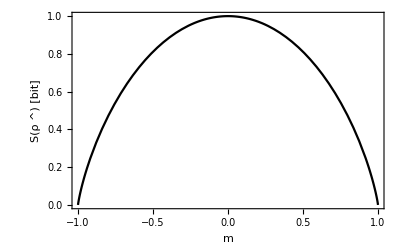

```mathematica
Plot[-((1+m)/2Log2[(1+m)/2]+(1-m)/2Log2[(1-m)/2]),{m,-1,1},PlotStyle->Black,FrameLabel->{"\!\(m\)","\!\(S(ρ\&^)\) [bit]"}]
```

Consider a generic single-qubit density matrix of the following form
 ρ̂=1/2(𝟙+m·σ),
where m is a three-component real vector. Calculate its von Neumann entropy S(ρ̂). Show that S(ρ̂)=0 when |m|=1, and S(ρ̂)=log 2 when |m|=0.

#### Purity and Rényi Entropy

Purity of a density matrix  ρ̂ quantify to which degree the density matrix is pure/mixed,

Tr (ρ̂)^2=∑_i p_i^2

By construction, Tr  (ρ̂)^2∈[0,1]. The criteria to determine if a density matrix  ρ̂ is pure or mixed is

ρ̂ is Piecewise[{{pure, if Tr  (ρ̂)^2=1,}, {mixed, if Tr  (ρ̂)^2<1.}}]

Rényi entropy of a density matrix  ρ̂

S^(n)(ρ̂)=1/(1-n)log Tr (ρ̂)^n.

In terms of the eigenvalues p_i of the density matrix  ρ̂,

S^(n)=(1-n)^-1 log ∑_i p_i^n.

n is the Rényi index.

n=0: max-entropy, simply counts the log of the Hilbert space dimension S^(0)=log dim ℋ.

n→1 limit: equivalent to the von Neumann entropy, i.e. S(ρ̂)=lim_(n→1) S^(n)(ρ̂).

Show that in the n→1 limit, the Rényi entropy reduces to the von Neumann entropy.

With Tr ρ̂=1, we can show

lim_(n→1) S^(n)(ρ̂)=lim_(n→1) 1/(1-n)ln Tr (ρ̂)^n
=-lim_(n→1) ∂_n ln Tr (ρ̂)^n
=-lim_(n→1) (Tr (ρ̂)^n ln ρ̂)/(Tr (ρ̂)^n)
=-(Tr ρ̂ ln ρ̂)/(Tr ρ̂)
=-Tr ρ̂ ln ρ̂=S(ρ̂).

n=2: the 2nd Rényi entropy is directly related to purity by S^(2)=-log Tr (ρ̂)^2.

n=∞: min-entropy, lower bound of all Rényi entropies, S^(∞)=-log max_i p_i.

The spectrum of the density matrix, i.e. all eigenvalues p_i, can be reconstructed from the family of Rényi entropies (by solving the following equations, in principle).

∑_i p_i^n=e^((1-n)S^(n))   (for n=1,2,…,dim ℋ).

#### Entropy and Knowledge

Entropy measures our ignorance about the quantum system. If we describe a quantum system by:

a pure state, we know that the system is in a definite quantum state ⇒ we have the full knowledge about the system ⇒ the system has no entropy, i.e. S^(n)(ρ̂)=0 (for all n).

a mixed state, there are several possible states that the system can take (we are not sure) ⇒ we only have partial knowledge about the system ⇒ our ignorance gives rise to the entropy of the system.

a maximally mixed state  ρ̂=𝟙/Tr ρ̂, we have no knowledge about the system, every state in the Hilbert space are equally likely ⇒  the entropy of the system is maximized.

The Rényi entropy (including the von Neumann entropy as a special case) can characterize how much the ensemble is mixed.

ρ̂ is Piecewise[{{pure, if S^(n)(ρ̂)=0,}, {mixed, if S^(n)(ρ̂)>0,}}] for n=1,2,….

Decoherence generally takes a pure state to a mixed state (unless the pure state is an energy eigenstate) and is the fundamental source of entropy production (to be explained later).

Jensen’s inequality: Rényi entropy is generally decreasing with the Rényi index,

ln dim ℋ=S^(0)≥S^(1)≥S^(2)≥…≥S^(∞)≥0.

The equality is achieved (simultaneously) if all p_i are equal.

∀i:p_i=1/(dim ℋ)⇒∀n≥0:S^(n)=log dim ℋ.

In this case, all Rényi entropies reach the maximum, and the ensemble is maximally mixed. The density matrix is proportional to identity matrix for maximally mixed ensemble.

ρ̂=1/(dim ℋ)𝟙.

Any quantum state can be realized with equal possibility in a maximally mixed ensemble ⇒ we are completely ignorant about the system ⇒ entropy is therefore maximized.

Maximally mixed qubit: We have no knowledge about the qubit ⇒ no preferred spin direction, i.e. ⟨σ⟩=0. Then according to Eq. (DisplayFormulaNumbered) (quantum state tomography),

ρ̂=𝟙/2≏1/2(1 | 0
0 | 1).

Application: if the qubit basis corresponds to the photon polarization, then the density matrix in Eq. (DisplayFormulaNumbered) describes the natural light ensemble of photons.

All Rényi entropies are identically log 2 for a maximally mixed qubit,

S^(n)=1/(1-n)log (1/2^n+1/2^n)=log 2=1bit.

This is the maximal entropy that a qubit could have: our ignorance about a qubit is at most 1 bit. This is why a qubit is called a quantum bit.

Let us conclude our discussion in the following table:

state ρ̂ | pure | ↔ | maximally mixed
purity Tr (ρ̂)^2 | 1 | ↔ | 1/dim ℋ
entropy S^(n)(ρ̂) | 0 | ↔ | log dim ℋ
knowledge | max | ↔ | none

## Quantum Entanglement

### Two-Qubit Systems

#### Tensor Product Hilbert Space

Composition of Systems: The Hilbert space of a combined quantum system is the direct product of the Hilbert space of each subsystem.

Two quantum systems A and B are associated with the Hilbert spaces ℋ_A and ℋ_B respectively,

ℋ_A=span{i_A}, ℋ_B=span{j_B},

the composite system A∪B will be associated with the Hilbert space

ℋ_(A∪B)=ℋ_A⊗ℋ_B=span{i_A⊗j_B}=span{ij}.

Hilbert space tensor product ⇒ Hilbert space dimension multiplies

dim ℋ_(A∪B)=dim ℋ_A dim ℋ_B.

Rule of scalar product: scalar product of two tensor product states equals the product of scalar products in each tensor Hilbert space

ijkl=j_B⊗i_Ak_A⊗l_B=ik_A jl_B=δ_ik δ_jl.

The tensor product basis is still orthonormal.

Generic states in ℋ_(A∪B)

v=∑_(i,j) v_ij ij.

where the vector element

v_ij=ijv.

Generic operators in ℋ_(A∪B)

Ô=∑_(i,j,k,l) ij(Ô)_(ij,kl)kl,

where the matrix (tensor) element

O_(ij,kl)=ij Ô kl.

Tensor product of states. Suppose u=∑_i u_i i_A, v=∑_j v_j j_B

u⊗v=∑_(i,j) u_i v_j i_A⊗j_B=∑_(i,j) u_i v_j ij.

Note: the double index ij labels a single state ij.

Take two qubits for example

(u_0
u_1)⊗(v_0
v_1)=(u_0(v_0
v_1)
u_1(v_0
v_1))=(u_0 v_0
u_0 v_1
u_1 v_0
u_1 v_1).

Tensor product of operators. Suppose A=∑_(i,j) i_A A_ij j_A, B=∑_(k,l) k_B B_kl l_B,

Â⊗B̂=∑_(i,j,k,l) A_ij B_kl i_A k_B j_A l_B
=∑_(i,j,k,l) A_ij B_kl ikjl.

Take two qubits for example

(A_00 | A_01
A_10 | A_11)⊗(B_00 | B_01
B_10 | B_11)
=(A_00(B_00 | B_01
B_10 | B_11) | A_01(B_00 | B_01
B_10 | B_11)
A_10(B_00 | B_01
B_10 | B_11) | A_11(B_00 | B_01
B_10 | B_11))
=(A_00 B_00 | A_00 B_01 | A_01 B_00 | A_01 B_01
A_00 B_10 | A_00 B_11 | A_01 B_10 | A_01 B_11
A_10 B_00 | A_10 B_01 | A_11 B_00 | A_11 B_01
A_10 B_10 | A_10 B_11 | A_11 B_10 | A_11 B_11).

#### Two-Qubit States

Each qubit has two basis states 0 and 1 (forming a 2-dim Hilbert space) ⇒ two qubits together have four basis states

|  | qubit B | 
 |  | 0 | 1
qubit A | 0 | 00 | 01
 | 1 | 10 | 11

The precise meaning of 00 is a tensor product of 0_A and 0_B states. In the vector representation,

00=0_A⊗0_B≏(1
0)⊗(1
0)=(1
0
0
0).

Similarly,

01=0_A⊗1_B≏(1
0)⊗(0
1)=(0
1
0
0),
10=1_A⊗0_B≏(0
1)⊗(1
0)=(0
0
1
0),
11=1_A⊗0_B≏(0
1)⊗(0
1)=(0
0
0
1).

These four basis states span the two-qubit Hilbert space.

A generic state in the two-qubit Hilbert space is a superposition of these four basis states,

ψ=ψ_0 00+ψ_1 01+ψ_2 10+ψ_3 11≏(ψ_0
ψ_1
ψ_2
ψ_3).

Normalization is still expected: ψψ=∑_i (|ψ_i|)^2=1.

Product state: a state that can be factorized as a tensor product of single-qubit states.

Suppose u=u_0 0+u_1 1 is a state of the first qubit and v=v_0 0+v_1 1 is a state of the second qubit. A two-qubit product state takes the general form of

u⊗v=(u_0 0+u_1 1)⊗(v_0 0+v_1 1)
=u_0 v_0 00+u_0 v_1 01+u_1 v_0 10+u_1 v_1 11.

The main feature of a product state is that each qubit behaves independently of the other: measurement or unitary operation of one qubit will not affect the other.

Not every state in the two-qubit Hilbert space can be written as product state. Why? Let us count the degrees of freedom:

A generic state as ψ in Eq. (DisplayFormulaNumbered) has six real parameters. 4×2-1-1=6.

A generic product state as u⊗v in Eq. (DisplayFormulaNumbered) has only four real parameters. (2×2-1-1)×2=4.

A generic state has more freedom than a product state, the additional freedom has to do with quantum entanglement.

Entangled state: any state that can not be factorized to product states are entangled.

Example: the state 1/(√2)(01-10) is entangled.

Prove that 1/(√2)(01-10) can not be written as a product state.

Prove by contradiction: If 1/(√2)(01-10) can be written as a product state, it must match Eq. (DisplayFormulaNumbered) that

u_0 v_0=0,u_0 v_1=1/(√2),u_1 v_0=-1/(√2),u_1 v_1=0.

Using the 1st and 4th equations, (u_0 v_0)(u_1 v_1)=0. Using the 2nd and 3rd equations (u_0 v_1)(u_1 v_0)=-1/2. u_0 u_1 v_0 v_1 can not be both 0 and -1/2 ⇒ contradiction.

Question: Is the state 1/2(00+01+10+11) entangled?

It is not obvious to see if a state is entangled or not ⇒ we need to develop measures of entanglement, such that by measuring these quantities, we can decide how much the state is entangled… (to be discussed later)

#### Two-Qubit Operators

Any physical observable of a two-qubit system is represented as a Hermitian operator acting on the two-qubit Hilbert space.

Single-qubit observables (each as a 3×4×4 tensor, extended from the 3×2×2 Pauli tensor):

(σ̂)_A=((σ̂)_A^x,(σ̂)_A^y,(σ̂)_A^z),
(σ̂)_B=((σ̂)_B^x,(σ̂)_B^y,(σ̂)_B^z).

Two-qubit observables (joint measurements, 3×3×4×4 tensor):

(σ̂)_A⊗(σ̂)_B=((σ̂)_A^x(σ̂)_B^x | (σ̂)_A^y(σ̂)_B^x | (σ̂)_A^z(σ̂)_B^x
(σ̂)_A^x(σ̂)_B^y | (σ̂)_A^y(σ̂)_B^y | (σ̂)_A^z(σ̂)_B^y
(σ̂)_A^x(σ̂)_B^z | (σ̂)_A^y(σ̂)_B^z | (σ̂)_A^z(σ̂)_B^z).

The precise meaning of (σ̂)_A^x (4×4 matrix):

(σ̂)_A^x⊗𝟙_B≏(0 | 1
1 | 0)⊗(1 | 0
0 | 1)=(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0).

The precise meaning of σ_A^z σ_B^y (4×4 matrix):

(σ̂)_A^z⊗(σ̂)_B^y≏(1 | 0
0 | -1)⊗(0 | -ⅈ
ⅈ | 0)=(0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0).

The single-qubit observables (σ̂)_A, (σ̂)_B, two-qubit observables (σ̂)_A⊗(σ̂)_B together with the identity observable 𝟙 (altogether 3+3+3×3+1=16 observables) form the complete set of observables for a two-qubit system, i.e. any physical observables of a two-qubit system must be a linear superposition of these 16 basis observables.

#### A Two-Qubit Model

Two-qubit Heisenberg model. Consider two qubits governed by the Hamiltonian

H=J/4 (σ̂)_A·(σ̂)_B=J/4(σ_A^x σ_B^x+σ_A^y σ_B^y+σ_A^z σ_B^z).

First write down the matrix representation,

H≏J/4(1 | 0 | 0 | 0
0 | -1 | 2 | 0
0 | 2 | -1 | 0
0 | 0 | 0 | 1).

Then diagonalize the Hamiltonian.

Eigenvalue E_s=-3J/4: a unique eigenstate ⇒ spin-singlet state

s=1/(√2)(01-10).

Eigenvalue E_t=J/4: three degenerated eigenstates ⇒ spin-triplet states (there is a basis freedom here, we make the following choice)

t_1=1/(√2)(01+10),
t_2=1/(√2)(00+11),
t_3=1/(√2)(00-11).

The lowest energy eigenstate is called the ground state, the rest of the eigenstates are excited states. In this model, assuming J>0, the ground state is the spin-singlet state.

#### The Spin-Singlet State

Use the vector representation of the spin-single state

s=1/(√2)(01-10)≏1/(√2)(0 | 1 | -1 | 0)ᵀ.

Expectation value of single-qubit observables

s(σ̂)_A s=(0,0,0),
s(σ̂)_B s=(0,0,0).

Expectation value of two-qubit observables

s(σ̂)_A⊗(σ̂)_Bs=(-1 | 0 | 0
0 | -1 | 0
0 | 0 | -1).

There is something unusual!

s is a pure state of the two-qubit system ⇒ the system is in a definite quantum state, entropy of the entire system = 0 ⇒ we have the full knowledge about the system.

However s(σ̂)_A s=0 implies nothing is know about qubit A, because qubit A is in a maximally mixed state with maximal entropy of the subsystem (1bit) ⇒ we are completely ignorant about the subsystems. (Same argument applies for qubit B)

The phenomenon that we may know everything about a quantum system yet nothing about its subsystems is a demonstration of quantum entanglement.

Classical information is stored locally (bit-by-bit) in every single classical bit. Knowing the entire system = knowing the state of every classical bit.

Quantum information can be stored jointly in the interrelations among qubits, but not locally in single qubits. Knowing the entire system does not imply the knowledge of its subsystem.

#### Entanglement Entropy

The entanglement entropy of the qubit A in a two-qubit state ψ is given by

S((ρ̂)_A)=-Tr (ρ̂)_A log (ρ̂)_A.

where  (ρ̂)_A is the reduced density matrix of qubit A obtained by tracing out qubit B in the full density matrix ψψ

(ρ̂)_A=Tr_B ψψ.

One may also define a more general Rényi version as

S^(n)((ρ̂)_A)=1/(1-n)log Tr (ρ̂)_A^n.

Example I: take the spin-singlet state

s=1/(√2)(↑↓-↓↑).

Full density matrix

ρ̂=ss≏1/2(0
1
-1
0)(0 | 1 | -1 | 0)=1/2(0 | 0 | 0 | 0
0 | 1 | -1 | 0
0 | -1 | 1 | 0
0 | 0 | 0 | 0).

Partial trace over qubit B ⇒ reduced density matrix of qubit A

(ρ̂)_A=Tr_B ss
≏1/2(tr(0 | 0
0 | 1) | tr(0 | 0
-1 | 0)
tr(0 | -1
0 | 0) | tr(1 | 0
0 | 0))=1/2(1 | 0
0 | 1).

Note that ρ_A indeed describes a maximally mixed qubit.

Compute the entropy of the reduced density matrix,

S( (ρ̂)_A)=-Tr (ρ̂)_A log (ρ̂)_A=log 2=1 bit.

Example II: take the product state

ψ=1/2(00+01+10+11).

Full density matrix

ρ̂=ψψ≏1/4(1
1
1
1)(1 | 1 | 1 | 1)=1/4(1 | 1 | 1 | 1
1 | 1 | 1 | 1
1 | 1 | 1 | 1
1 | 1 | 1 | 1).

Partial trace over qubit B ⇒ reduced density matrix of qubit A

(ρ̂)_A=Tr_B ρ̂
≏1/4(tr(1 | 1
1 | 1) | tr(1 | 1
1 | 1)
tr(1 | 1
1 | 1) | tr(1 | 1
1 | 1))=1/2(1 | 1
1 | 1).

Compute the entropy of the reduced density matrix,

S( (ρ̂)_A)=-Tr  (ρ̂)_A log  (ρ̂)_A=-(0log 0+1 log 1)=0 bit.

Conclusion: The entanglement entropy characterizes the amount of quantum entanglement between subsystem A and its complement Ā (which is B here), given that the full system A∪Ā is pure.

pure state ψ | product | ↔ | maximally entangled
(ρ̂)_A | pure | ↔ | maximally mixed
EE S^(n)( (ρ̂)_A) | 0 | ↔ | log dim ℋ_A
entanglement | none | ↔ | max

For diagnostic purpose (to distinguish product state from entangled state), any Rényi index n=1,2,... will work.

Why entropy provides a measure of entanglement? Quantum entanglement: the nonlocal nature of quantum information in an entangled state (i.e. information shared jointly among subsystems) ⇒ separating out a subsystem would lead to lost of information ⇒ hence the production of (entanglement) entropy.

Open questions: The system must be pure, otherwise there are other source of entropy productions. What about entanglement in a mixed state? Good to describe bipartite entanglement. What about multipartite entanglement?

#### EPR Pair and Bell Inequality

Bell states: maximally entangled pure states of two qubits. Also known as Einstein-Podolsky-Rosen (EPR) pair states. The spin-singlet state in Eq. (DisplayFormulaNumbered) is one example:

EPR=1/(√2)(01-10).

Suppose a machine can repeatedly prepare such EPR pairs and distribute the qubits separately to Alice and Bob,

```mathematica
Graphics[{{LightGray,Disk[{0,5},{6,1}]},Text["EPR state",{0,5}],{Arrowheads[{{0.1,0.8}}],Arrow[{{0,0},{5,5}}],Arrow[{{0,0},{-5,5}}]},{Disk[#,0.5]&/@{{-5,5},{5,5}}},{EdgeForm[Black],LightGray,Rectangle[{-1,-1},{1,1},RoundingRadius->.5]},
{Text["Alice",{-5,5},{0,-1.2}],Text["Bob",{5,5},{0,-1.2}],Text["source",{0,-1},{0,1}]}},ImageSize->120]
```

-Graphics-

Alice and Bob can measure their own qubit and record the measurement outcome. After the measurement, the pair of qubits are discarded. New EPR pairs will be acquired from the source.

Alice defines her set of observables:

(σ̂)_A=((σ̂)_A^x,(σ̂)_A^y,(σ̂)_A^z).

Bob defines his set of observables:

(σ̂)_B=((σ̂)_B^x,(σ̂)_B^y,(σ̂)_B^z).

The observables are perfectly anti-correlated between Alice and Bob

EPR(σ̂)_A EPR=EPR(σ̂)_B EPR=(0,0,0),
EPR(σ̂)_A⊗(σ̂)_BEPR=(-1 | 0 | 0
0 | -1 | 0
0 | 0 | -1).

If Alice and Bob both measure σ^z, they will find

σ_A^z=-σ_B^z=Piecewise[{{+1, p=1/2}, {-1, p=1/2}}].

Quantum explanation: can be inferred from ⟨σ_A^z⟩=⟨σ_B^z⟩=0 and ⟨σ_A^z σ_B^z⟩=-1.

This is not too surprising: just a perfect anti-correlation between two random variables. Classically, one may model the perfect anti-correlation by a hidden variable:

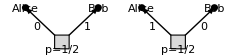

```mathematica
Block[{bg,str},
bg={{Arrowheads[{{0.05,0.85}}],Arrow[{{0,0},{5,5}}],Arrow[{{0,0},{-5,5}}]},{Disk[#,0.5]&/@{{-5,5},{5,5}}},{EdgeForm[Black],LightGray,Rectangle[{-1,-1},{1,1},RoundingRadius->.5]},
{Text["Alice",{-5,5},{0,-1.2}],Text["Bob",{5,5},{0,-1.2}]},
Text["\!\(p=1/2\)",{0,-1},{0,1}]};
str[bs_]:=Inset[Grid[{#1},Alignment->{Center,Center},Frame->All,FrameStyle->Thin,Spacings->{0.05,0}],{#2,3},{-Sign[#2],1}]&@@@Thread[{bs,{-3,3}}];
Graphics[{Translate[{bg,str[{{"0"},{"1"}}]},{-8,0}],Translate[{bg,str[{{"1"},{"0"}}]},{8,0}]},ImageSize->240]]
```

If Alice and Both both measure σ^x, they will find

σ_A^x=σ_B^x=Piecewise[{{+1, p=1/2}, {-1, p=1/2}}].

Quantum explanation: can be inferred from ⟨σ_A^x⟩=⟨σ_B^x⟩=0 and ⟨σ_A^x σ_B^x⟩=1.

To model this classically: we will need to introduce another hidden variable to encode the perfect correlation in σ^x channel.

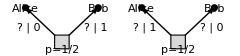

```mathematica
Block[{bg,str},
bg={{Arrowheads[{{0.05,0.85}}],Arrow[{{0,0},{5,5}}],Arrow[{{0,0},{-5,5}}]},{Disk[#,0.5]&/@{{-5,5},{5,5}}},{EdgeForm[Black],LightGray,Rectangle[{-1,-1},{1,1},RoundingRadius->.5]},
{Text["Alice",{-5,5},{0,-1.2}],Text["Bob",{5,5},{0,-1.2}]},
Text["\!\(p=1/2\)",{0,-1},{0,1}]};
str[bs_]:=Inset[Grid[{#1},Alignment->{Center,Center},Frame->All,FrameStyle->Thin,Spacings->{0.05,0}],{#2,3},{-Sign[#2],1}]&@@@Thread[{bs,{-3,3}}];
Graphics[{Translate[{bg,str[{{"?","0"},{"?","1"}}]},{-8,0}],Translate[{bg,str[{{"?","1"},{"?","0"}}]},{8,0}]},ImageSize->240]]
```

As Alice and Bob can choose to measure either σ^z or σ^x at their free will ⇒ Classically, both hidden variables about σ^z and σ^x must be sent with the qubit. (Although a single EPR state is sufficient to explain all situations in the quantum way).

If Alice measures σ_A^z and Bob measures σ_B^x, they will find independently that

σ_A^z=Piecewise[{{+1, p=1/2}, {-1, p=1/2}}], σ_B^x=Piecewise[{{+1, p=1/2}, {-1, p=1/2}}].

Quantum explanation: can be inferred from ⟨σ_A^z⟩=⟨σ_B^x⟩=0 and ⟨σ_A^z σ_B^x⟩=0.

The classical hidden variables can reproduce this behavior only if they follow the joint distribution

Alice | Bob | p
00 | 11 | 1/4
01 | 10 | 1/4
10 | 01 | 1/4
11 | 00 | 1/4

So far so good. But Alice and Bob can also decide to measure σ^y, or more generally, any linear combination of their observables … What if Alice measures n_A·σ_A and Bob measures n_B·σ_B? (where n_A and n_B are unit vectors) Their outcomes will follow the joint distribution

n_A·σ_A | n_B·σ_B | p
+1 | -1 | (1+n_A·n_B)/4
+1 | +1 | (1-n_A·n_B)/4
-1 | -1 | (1-n_A·n_B)/4
-1 | +1 | (1+n_A·n_B)/4

The probability that Alice and Bob obtain the same outcome is

p(n_A·σ_A=n_B·σ_B)=(1+n_A·n_B)/2.

Quantum explanation: can be inferred from ⟨n_A·σ_A⟩=⟨n_B·σ_B⟩=0 and ⟨n_A·σ_An_B·σ_B⟩=n_A·n_B.

Classically, to reproduce all these, we will need many (could be infinitely many) hidden variables. (This is ugly but not fatal yet.)

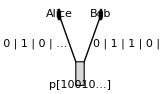

```mathematica
Block[{bg,str},
bg={{Arrowheads[{{0.12,0.85}}],Arrow[{{0,0},{5,5}}],Arrow[{{0,0},{-5,5}}]},{Disk[#,0.5]&/@{{-5,5},{5,5}}},{EdgeForm[Black],LightGray,Rectangle[{-1,-1},{1,1},RoundingRadius->.5]},
{Text["Alice",{-5,5},{0,-1.2}],Text["Bob",{5,5},{0,-1.2}]}};
str[bs_]:=Inset[Grid[{#1},Alignment->{Center,Center},Frame->All,FrameStyle->Thin,Spacings->{0.05,0}],{#2,3},{-Sign[#2],1}]&@@@Thread[{bs,{-3,3}}];
Graphics[{bg,str[{{"1","0","0","1","0","…"},{"0","1","1","0","1","…"}}],Text["\!\(p[10010…]\)",{0,-1},{0,1}]},ImageSize->160]]
```

There should be complicated correlation among hidden variables in an attempt to match quantum predictions (but the attempt may fail). Suppose two of the hidden variables happen to determine the outcome of n_1·σ and n_2·σ. After marginalizing (summing) over all the other hidden variables, the marginal distribution should be

Alice | Bob | p
…00… | …11… | (1+n_1·n_2)/4
…01… | …10… | (1-n_1·n_2)/4
…10… | …01… | (1-n_1·n_2)/4
…11… | …00… | (1+n_1·n_2)/4.

Now consider Alice and Bob can choose to measure any one of the three observables n_1·σ, n_2·σ and n_3·σ (on their own qubits respectively, where n_(1,2,3) are unit vectors).

Classically, there must be three hidden variables associated with the three observables, following some marginal distribution

Alice | Bob | p
…000… | …111… | p_1
…001… | …110… | p_2
…010… | …101… | p_3
…011… | …100… | p_4
…100… | …011… | p_5
…101… | …010… | p_6
…110… | …001… | p_7
…111… | …000… | p_8.

The probability must sum up to 1, i.e.

p_1+p_2+…+p_8=1.

If Alice measures n_1·σ_A and Bob measures n_2·σ_B, the probability that they obtain the opposite outcome is

p(n_1·σ_A=-n_2·σ_B)=p_1+p_2+p_7+p_8.

If Alice measures n_2·σ_A and Bob measures n_3·σ_B, the probability that they obtain the opposite outcome is

p(n_2·σ_A=-n_3·σ_B)=p_1+p_4+p_5+p_8.

If Alice measures n_3·σ_A and Bob measures n_1·σ_B, the probability that they obtain the opposite outcome is

p(n_3·σ_A=-n_1·σ_B)=p_1+p_3+p_6+p_8.

Put together,

p(n_1·σ_A=-n_2·σ_B)+p(n_2·σ_A=-n_3·σ_B)+p(n_3·σ_A=-n_1·σ_B)
=3 p_1+p_2+p_3+p_4+p_5+p_6+p_7+3 p_8
=1+2 p_1+2 p_8

This leads to a (version of) Bell inequality.

p(n_1·σ_A=-n_2·σ_B)+p(n_2·σ_A=-n_3·σ_B)+p(n_3·σ_A=-n_1·σ_B)≥1.

Now what is the quantum mechanical prediction? Recall the quantum result in Eq. (DisplayFormulaNumbered), the Bell inequality would require

(1+n_1·n_2)/2+(1+n_2·n_3)/2+(1+n_3·n_1)/2≥1,

for three unit vectors n_1, n_2 and n_3.

Consider a special case, where the three vectors are 120° to each other in a plane.

```mathematica
Graphics[{Arrowheads[0.2],{Arrow[{{0,0},#1}],Text["\!\(n\_"<>#2<>"\)",#1,-#1]}&@@@Thread[{CirclePoints[3],ToString/@Range[3]}]},ImageSize->80]
```

-Graphics-

n_1·n_2=n_2·n_3=n_3·n_1=-1/2.

Then Eq. (DisplayFormulaNumbered) would require

1/4+1/4+1/4=3/4≥1,

which is not true.

The violation of the Bell inequality indicates that no classical model of local hidden variables can ever reproduce all the predictions of quantum mechanics. This is the Bell’s theorem.

John S. Bell (1928-1990)

The Nobel (no-Bell) Prize in Physics 2022
“for experiments with entangled photons, establishing the violation of Bell inequalities and pioneering quantum information science”
 |  | 
Alain Aspect | John F. Clauser | Anton Zeilinger

How does Bell inequality tell us about entanglement?

Consider a two qubit state, parametrized by a phase angle α,

ψ=cos α01-sin α10≏(0
cos α
-sin α
0).

```mathematica
ψ={0,Cos[α],-Sin[α],0};
```

There are two limits:

α=π/4 ⇒ cos α=sin α=1/(√2) ⇒ ψ=1/(√2)(01-10) is the EPR state (maximally entangled).

α=0 ⇒ cos α=1 and sin α=0 ⇒ ψ=01 reduces to the product state (no entanglement).

As α is tuned between these two limit, the amount of quantum entanglement can be adjusted. There must be a point where the amount of entanglement (“quantumness”) is no longer sufficient to support the violation of the Bell inequality.

Entanglement entropy

S((ρ̂)_A)=-cos^2α log cos^2 α-sin^2 α log sin^2 α

```mathematica
ρ=ψ⊗ψ;
ρA=TensorContract[ArrayReshape[ρ,{2,2,2,2}],{{2,4}}];
SA=Total[-# Log[#]&/@Eigenvalues@ρA]
```

-Cos[α]^2 Log[Cos[α]^2]-Log[Sin[α]^2] Sin[α]^2

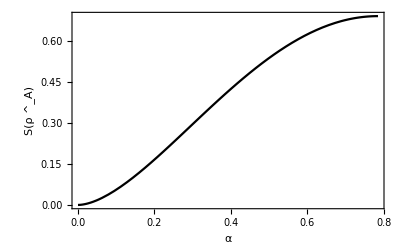

```mathematica
Plot[SA,{α,0,π/4},FrameLabel->{"\!\(α\)","\!\(S(ρ\&^\_A)\)"},PlotStyle->Black]
```

Observable expectation values

ψ(σ̂)_A ψ=(0,0,cos 2α),
ψ(σ̂)_B ψ=(0,0,-cos 2α),
ψ(σ̂)_A⊗(σ̂)_Bψ=(-sin 2α | 0 | 0
0 | -sin 2α | 0
0 | 0 | -1).

```mathematica
Table[ψ.KroneckerProduct[PauliMatrix[a],PauliMatrix[b]].ψ,{a,0,3},{b,0,3}]//FullSimplify//TableForm
```

1 | 0 | 0 | -Cos[2 α]
0 | -Sin[2 α] | 0 | 0
0 | 0 | -Sin[2 α] | 0
Cos[2 α] | 0 | 0 | -1

If Alice measures n_1·σ_A and Bob measures n_2·σ_B, the probability for their measurement outcomes to be opposite is given by

p(n_1·σ_A=-n_2·σ_B)=ψ(𝒫̂)_(n_1·σ_A=-n_2·σ_B)ψ,

where the projection operator (𝒫̂)_(n_1·σ_A=-n_2·σ_B) is given by

(𝒫̂)_(n_1·σ_A=-n_2·σ_B)=∑_(s=±1) (𝒫̂)_(n_1·σ_A=s)(𝒫̂)_(n_2·σ_B=-s)
=∑_(s=±1) (𝟙+s n_1·(σ̂)_A)/2(𝟙-s n_2·(σ̂)_B)/2
=(𝟙- n_1·((σ̂)_A⊗(σ̂)_B)·n_2)/2.

Therefore

p(n_1·σ_A=-n_2·σ_B)=(1- n_1·ψ(σ̂)_A⊗(σ̂)_Bψ·n_2)/2.

Suppose the unit vectors n_1, n_2, n_3 are still placed in the xz-plane with 120° to each other

n_1=(cos θ,0,sin θ),
n_2=(cos(θ+2π/3),0,sin(θ+2π/3)),
n_2=(cos(θ-2π/3),0,sin(θ-2π/3)).

Then the left-hand-side (l.h.s.) of the Bell inequality reads

p(n_1·σ_A=-n_2·σ_B)+p(n_2·σ_A=-n_3·σ_B)+p(n_3·σ_A=-n_1·σ_B)
=3/8(3-sin 2α).

```mathematica
Simplify@Total[(1-#1.DiagonalMatrix[{-Sin[2α],-1}].#2)/2&@@@Thread@{#,RotateLeft[#]}&@CirclePoints[{1,θ},3]]
```

-3/8 (-3+Sin[2 α])

It turns out that this result is independent of the choice of θ.

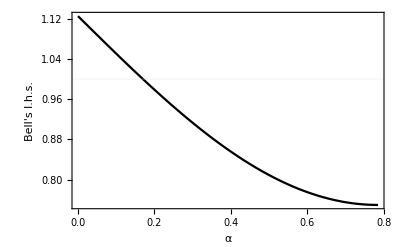

```mathematica
Plot[3/8(3-Sin[2α]),{α,0,π/4},FrameLabel->{"\!\(α\)","Bell's l.h.s."},PlotStyle->Black,GridLines->{None,{1}}]
```

We can plot the l.h.s. of the Bell inequality v.s. the 2nd Rényi entanglement entropy for different α:

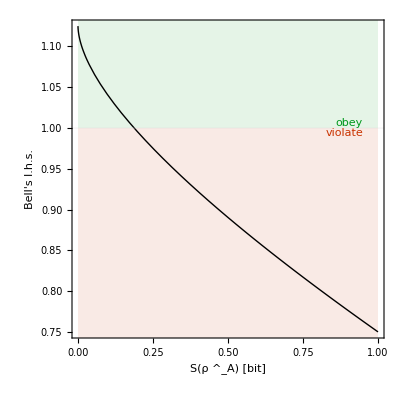

```mathematica
ParametricPlot[{SA/Log[2],3/8(3-Sin[2α])},{α,0,π/4},AspectRatio->1,PlotStyle->Black,PlotRangePadding->0.01,Prolog->{Opacity[0.1],{Red,Polygon[{{0,1},{1,1},{1,0},{0,0}}]},{Green,Polygon[{{0,1},{1,1},{1,2},{0,2}}]}},GridLines->{None,{1}},
FrameLabel->{"\!\(S(ρ\&^\_A)\) [bit]","Bell's l.h.s."},
Epilog->{{Red,Text["violate",{0.95,1},{1,1}]},{Green,Text["obey",{0.95,1},{1,-1}]}}]
```

For pure state, such as ψ in the above example, entanglement entropy S((ρ̂)_A)>0 as long as α>0 ⇔ the state is entangled. But the Bell inequality is not always violated. ⇒ It is an entanglement witness.

For mixed state, entropy no longer provides a good measure of quantum entanglement. We had to rely on Bell inequalities and other entanglement witness.